Run the following line to add the package to the path (unless this has already been done)

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

Now we can load the package

```mathematica
<<RiemannHilbert`;
```

PainleveII[{s1,s2,s3},x]  evaluates the solution to Painleve II with Stokes' constants s1, s2 and s3 at the point x.  

	It should be accurate for all x on the real axis.

	We have aimed for an accuracy of 10.^(-7).  
		
Implementation notes:


	For x close to zero, the routine uses the method developed in [Olver 2009b], and should take roughly 5 seconds for the first usage, and less than 2 seconds for any subsequent evaluations.
	
	For x away from zero, we use deformed contours based on [Fokas et al., 2006].  Special contours are needed for the case s_1 s_3=1 and x negative, and s_2=0 and x positive (the Ablowitz–Segur solutions).  Note that Hastings–McLeod solution is the solution that satisfies both s_1 s_3=1 and s_2=0.
	
	To speed up the algorithm, we store precomputed matrices.  Evaluate

```mathematica
ClearPainleveDatabase[]
```

To remove these stored matrices and free up the memory.

## Ablowitz–Segur solutions

We compute solutions which are asymptotic to α Ai[z].  This is equivalent to the Stokes' constants (-ⅈ α,0,ⅈ α).

```mathematica
s//Clear;
s[α_]:={-I α,0,I α};
```

We save the computation — in case you wish to extend or refine the graphs without starting from scratch — as the method is still fairly slow

```mathematica
Clear[p];
p[α_,x_]:=p[α,x]=PainleveII[s[α],x]
```

### Example solutions

Two solutions near the Hastings–McLeod solution (but with drasticly different behaviour)

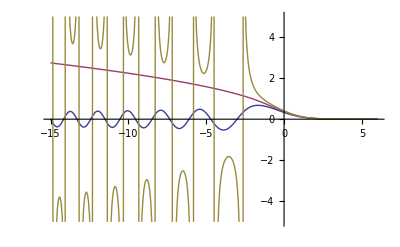

```mathematica
Monitor[TablePlot[{p[.9,x]//Re,p[1.,x]//Re,p[1.1,x]//Re},{x,-15.,6.,2.^(-4)},PlotRange->{-5,5}],x]
```

Here's two oscillatory solutions for large negative x

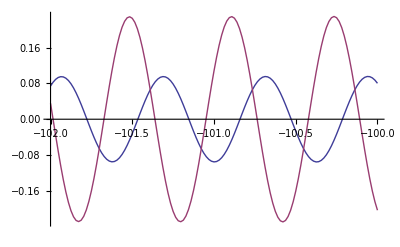

```mathematica
Monitor[TablePlot[{p[.5,x]//Re,p[.9,x]//Re},{x,-102.,-100.,2.^(-6)}],x]
```

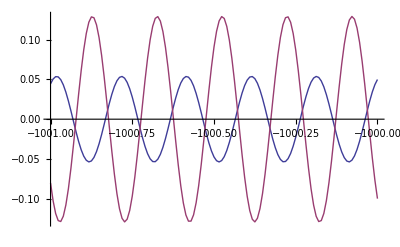

```mathematica
Monitor[TablePlot[{p[.5,x]//Re,p[.9,x]//Re},{x,-1001.,-1000.,2.^(-7)}],x]
```

And here's two exploding solutions for large negative x

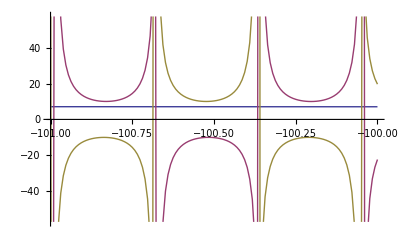

```mathematica
Monitor[TablePlot[{p[1.,x]//Re,p[1.1,x]//Re,p[1.5,x]//Re},{x,-101.,-100.,2.^(-7)}],x]
```

### Error in Hastings–McLeod

We can compare p[0,x] with the Prahofer and Spohn data values

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

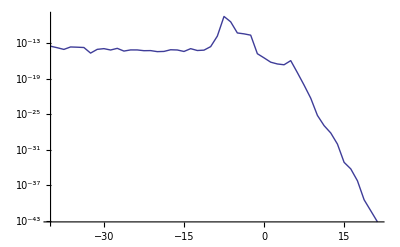

```mathematica
Monitor[Block[{x},
ListLineLogPlot[{x=#⟦1⟧,p[1.,x]+#⟦3⟧//Abs}&/@data⟦;;1000;;20⟧,PlotRange->All]
],x]
```

We achieve high accuracy.  Here’s the relative error:

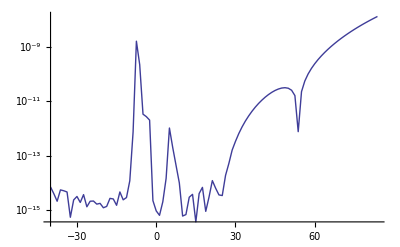

```mathematica
Monitor[Block[{x},
{x=#⟦1⟧,(p[1.,x]+#⟦3⟧)/(#⟦3⟧)//Abs}&/@data⟦;;2000;;20⟧//ListLineLogPlot
],x]
```

Further optimization of the PainleveII routine should improve the accuracy in the future

### Comparison with asymptotics

For 0 < α < 1, we have the following asymptotic approxiamtion:

```mathematica
d[α_]:=Sqrt[-1/π Log[1-α^2]];
θ2[α_]:=π/4-3/2 d[α]^2 Log[2] - Arg[Gamma[1-(I d[α]^2)/2]];
asym[α_,z_]:=d[α](-z)^(-1/4)Sin[2/3(-z)^(3/2)-3/4 d[α]^2 Log[-z]+θ2[α]];
```

We see that the asymptotic approximation is indeed asymptotic to our computed solution

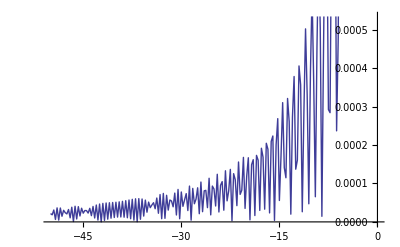

```mathematica
Monitor[TablePlot[(asym[0.5,x]-p[0.5,x])//Abs,{x,-50.,-5.,1./2^2}],x]
```

### Varying α

As x becomes very negative, the Hastings–McLeod solution becomes increasingly unstable.  We demonstrate this by fixing x = 0.–10,-1000 and varying α

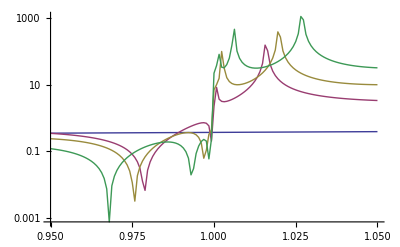

```mathematica
Monitor[TableLogPlot[{p[α,0.]//Abs,p[α,-10.]//Abs,p[α,-100.]//Abs,p[α,-1000.]//Abs},{α,.95,1.05,1./(10 2^7)},PlotRange->All],α]
```

The (smooth) jump at α = 1 becomes increasingly stiff as a pole and a zero approach the real axis

## Real-valued example

Here's another example where we know for sure that the solution is real

```mathematica
p2[x_]:=p2[x]=PainleveII[{1+I,-2,1-I},x];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {« 1 »} may contain significant numerical errors.

General::stop: Further output of LinearSolve :: luc will be suppressed during this calculation.

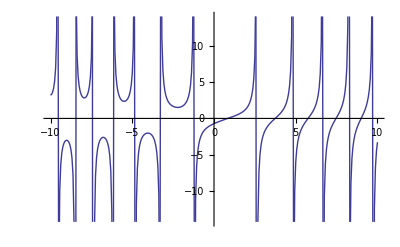

```mathematica
Monitor[TablePlot[p2[x]//Re,{x,-10.,10.,2.^(-4)}],x]
```

PainleveII uses the undeformed contour for positive x less than 8.  This contour is inherently ill-conditioned, resulting in a badly condition linear system, until it switches to the deformed contour.  Future versions of RHPackage will use a deformed contour for this regime as well.  For very large x, the deformed contour is well conditioned:

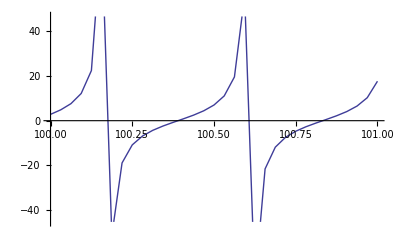

```mathematica
Monitor[TablePlot[p2[x]//Re,{x,100.,101.,2.^(-5)}],x]
```

## Complex-valued example

Here's an example where the solution is complex valued

```mathematica
p3[x_]:=p3[x]=PainleveII[{1,2,1/3},x];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {« 1 »} may contain significant numerical errors.

General::stop: Further output of LinearSolve :: luc will be suppressed during this calculation.

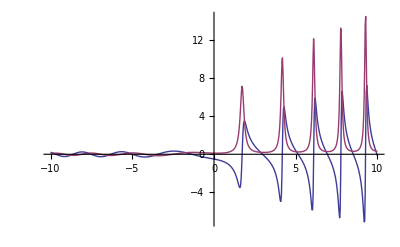

```mathematica
Monitor[ReImTablePlot[p3[x],{x,-10.,10.,2.^(-5)},PlotRange->All],x]
```

At large positive x, the solution continues to have pulse-like behaviour

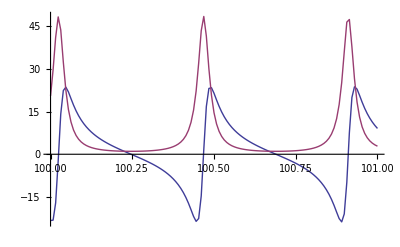

```mathematica
Monitor[ReImTablePlot[p3[x],{x,100.,101.,2.^(-7)},PlotRange->All],x]
```

## Perturbations of Hastings–McLeod

Above, we investigated the Ablowitz–Segur solutions; essentially, perturbations of the initial conditions of the Hastings–McLeod solution at +∞

Here, we investigate perturbations of the Hastings–McLeod solution at –∞.  This is equivalent to choosing s_1 s_3=1.  These conditions ensure that

	s_1-s_2+s_3+s_1 s_2 s_3=s_1+s_3=0
	
Therefore, s_2 can be arbitrary.  On the other hand, s_1=-s_3, and therefore s_1=±ⅈ.  The Hastings–McLeod solution we plotted before corresponds to s_1=ⅈ.

```mathematica
pHM//Clear;pHM[s2_,x_]:=pHM[s2,x]=PainleveII[{I,s2,-I},x];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {« 1 »} may contain significant numerical errors.

General::stop: Further output of LinearSolve :: luc will be suppressed during this calculation.

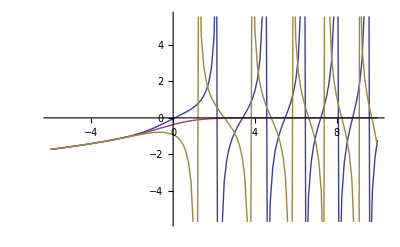

```mathematica
Monitor[Show[TablePlot[{pHM[-2.,x]//Re,pHM[0.,x]//Re,pHM[2.,x]//Re},{x,-6.,0.,1./2^1}],TablePlot[{pHM[-2.,x]//Re,pHM[0.,x]//Re,pHM[2.,x]//Re},{x,0.,10.,1./2^3}],PlotRange->All],x]
```

## References

A. S. Fokas, A. R. Its, A. A. Kapaev & V. Yu. Novokshenov (2006), Painlevé Transcendents: the Riemann–Hilbert approach, AMS. 

S. Olver (2010), A general framework for solving Riemann–Hilbert problems numerically, Report no. NA-10/5, Mathematical Institute, Oxford University.

S. Olver (2009b), Numerical solution of Riemann–Hilbert problems: Painlevé II, to appear in Found. Comput. Maths.

S. Olver (2009a), Computing the Hilbert transform and its inverse, to appear in Maths Comp.